# -Graphics-

# New Features in the Wolfram Language 12.2

-Graphics-

## Summary

228 new functions

Two new computational domains

Many enhancements to existing functionality

Some UI improvements

## New Domain: Spatial Statistics

Statistics: Data comes from a fixed distribution.

Random processes: The distribution depends on what happened before.

Spatial statistics: The distribution depends on where other points are.

## Spatial Statistics: Key Ideas

Models that describe repulsion and attraction

Estimate expected separation, density, center, etc.

Simulate data or estimate models

Test cluster and uniformity

### Applications

Environmental studies, population health, biosciences, geology, materials physics…

### Examples

#### Statistics

```mathematica
RandomVariate[
DiscreteUniformDistribution[{1,6}],
50]
```

```mathematica
ListPlot[%]
```

#### Processes

```mathematica
data=RandomFunction[
BinomialProcess[1/3],
{0,50}]
```

```mathematica
ListPlot[data,Filling->Axis]
```

#### Spatial statistics

```mathematica
pts=RandomPointConfiguration[
MaternPointProcess[10,20,.1,2],
Disk[]]
```

```mathematica
Show[RegionPlot[pts["ObservationRegion"]],ListPlot[pts]]
```

```mathematica
pts["Properties"]
```

Probability that space is not empty:

```mathematica
EmptySpaceF[pts,0.02]
```

Expected number of points within 0.05 of a typical point:

```mathematica
pts["MeanPointDensity"]RipleyK[pts,0.05]
```

Estimate processes from data:

```mathematica
EstimatedPointProcess[pts,MaternPointProcess[μ,λ,a,b]]
```

## New Domain: BioSequence

Symbolic representation of DNA, circular DNA, RNA and peptides

Modification and conversion tools

Sequence comparison tools

Integration with molecular computations

Integration with the Wolfram Knowledgebase™

### Applications

Medicine

Agriculture

Environmental science

Anthropology

### Examples

```mathematica
seq=BioSequence["ACGGG"]
```

```mathematica
seq["MolecularMass"]
```

```mathematica
BioSequenceTranslate[seq]
```

```mathematica
mol=Molecule[seq]
```

```mathematica
MoleculePlot3D[mol]
```

```mathematica
factorV=BioSequence[Entity["Gene",{"F5",{"Species"->"HomoSapiens"}}]]
```

```mathematica
BioSequence[Entity["Gene",{"Arl6ip6",{"Species"->"RattusNorvegicus"}}]]
```

```mathematica
LongestCommonSubsequence[factorV,BioSequence[Entity["Gene",{"Arl6ip6",{"Species"->"RattusNorvegicus"}}]]]
```

## Graphics

### Performance

2D Graphics Manipulate/Animation/Dynamic with larger image size
12.1: average 15 fps
12.2: average 23 fps

2D Polygon with VertexColors 
12.1: 3844 ms to render 
12.2: 640 ms to render

Zoom in large Raster/Image
12.1: average .6 fps
12.2: average 13 fps

Multiple GeometricTransformation
12.1: 1.5 fps
12.2: 27 fps

```mathematica
Graphics3D[Translate[Cuboid[],Flatten[Table[{i,j,k},{i,25},{j,25},{k,25}],2]]]
```

-Graphics3D-

Raster3D/Image3D together with transparent 3D objects (bounded volume rendering)
12.1: 12 fps
12.2: 38 fps

```mathematica
Show[Import["ExampleData/CTengine.tiff","Image3D"],Graphics3D[{Opacity[.5],Red,Sphere[{15,15,15},10]}]]
```

-Graphics3D-

### New Plot Types

#### Multi-axis plots

View data with multiple parameters:

```mathematica
RadialAxisPlot[{9,7,9,5,5,7}]
```

```mathematica
RadialAxisPlot[{Legended[<|"Marketing"->9,"Development"->7,"Admin"->9,"Sales"->5,"Support"->5|>,"Budget"],
Legended[<|"Marketing"->4,"Development"->7,"Admin"->8,"Sales"->6,"Support"->7|>,"Spent"]}]
```

```mathematica
ParallelAxisPlot[RandomChoice[Range[10],{5 ,5}]]
```

#### PointValuePlot

```mathematica
PointValuePlot[Table[RandomReal[10,2]->{RandomReal[],RandomChoice[{1,2,3}]},20],PlotLegends->Automatic]
```

-Graphics-

```mathematica
PointValuePlot[Table[RandomGeoPosition[LinguisticAssistant]->{RandomInteger[3],RandomReal[100]},20],PlotLegends->Automatic]
```

-Graphics-

#### Image analysis

```mathematica
ImageWaveformPlot[-Graphics-]
```

-Graphics-

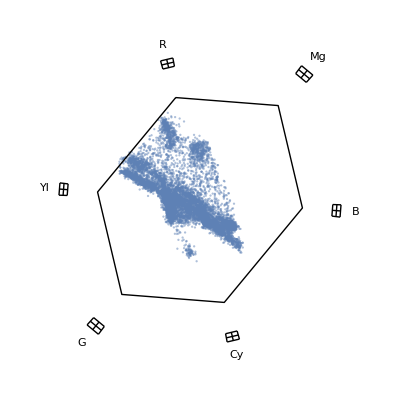

```mathematica
ImageVectorscopePlot[-Graphics-]
```

#### ArrayPlot3D

```mathematica
ArrayPlot3D[CellularAutomaton["GameOfLife",RandomInteger[1,{50,50}],50]]
```

-Graphics3D-

### Improved Aesthetics

#### 3D vectors

```mathematica
SliceVectorPlot3D[{y,-x,z}, {x^2-y^2-z==0},{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

#### More support for texture & shading

Sphere, Cylinder, Cuboid, Cone, BSplineSurface, Tube, Rectangle, Disk:

```mathematica
Manipulate[Graphics[{SurfaceAppearance["HHH"],Texture[ExampleData[{"TestImage","Sailboat"}]],Rotate[Disk[{0,0},{1,1},{r1,r2}],angle,{0,0}]},PlotRange->1],{{r1,0},0,Pi*2},{{r2,1},0,Pi*2},{angle,0,Pi*2}]
```

#### More shaders

```mathematica
Plot[2Sin[x]+x,{x,0,15},FillingStyle->LinearGradientFilling[{RGBColor[1., 0.71, 0.75],RGBColor[0.64, Rational[182, 255], Rational[244, 255]]},Top],Filling->Bottom]
```

-Graphics-

```mathematica
SectorChart[Tuples[{1,2},2],ChartStyle->ConicGradientFilling["Pastel",ImageScaled[{0.5,0.5}]],]
```

```mathematica
GeoGraphics[{RadialGradientFilling[{RGBColor[0.6705882352941176, 0.8627450980392157, 1.],RGBColor[0.011764705882352941, 0.5882352941176471, 1.]}],Polygon[LinguisticAssistant]},GeoBackground->None]
```

#### Ray tracing [experimental, macOS only]

```mathematica
Style[
Graphics3D[,
Boxed->False,ImageSize->Large,
 ViewPoint->{0,0,3}, ViewVertical->{0,1,0}, Lighting->{{"Area",White,{0,1.9,0}, {{0.2,0.0,0}, {0,0,0.3}}}}, Method->{"RayTracing" -> {"ImageSamples" ->100, "RayBounces" -> 3}}], RenderingOptions->{"3DRenderingMethod"->#} ]&/@{ Automatic,"RayTracing"}
```

{-Graphics3D-,-Graphics3D-}

## Vector GeoGraphics

### Crisp Detail

```mathematica
GeoGraphics[Entity["Building","TowerOfLondon::956p9"],GeoZoomLevel->17,ImageSize->800]
```

-Graphics-

```mathematica
a=GeoGraphics[Entity["Building","TowerOfLondon::956p9"],GeoZoomLevel->17,GeoBackground->"VectorClassic",ImageSize->800]
```

-Graphics-

### Element Meaning

```mathematica
c=DeleteCases[
DeleteCases[a,
(Annotation[_,{_String,t2_String,_String},___]/;(t2=!="building"))
|_Inset
|_Text,∞],
Rotate[_Real,_],∞]
```

-Graphics-

```mathematica
GeoGraphicsVectorExplorer[GeoGraphics[Entity["City",{"Seoul","Seoul","SouthKorea"}],ImageSize->{800,1000},GeoProjection->"Mercator",GeoBackground->"VectorDefault"]]
```

### Eight Styles

```mathematica
GeoGraphics[Entity["City",{"NewYork","NewYork","UnitedStates"}],GeoBackground->"VectorVintage",ImageSize->800]
```

### Non-clashing Undistorted Labels

```mathematica
map[background_]:=GeoGraphics[GeoBackground->background,GeoRange->"World",ImageSize->800,GeoBackground->"StreetMap",GeoProjection->"Mollweide",GeoGridRangePadding->0.1];
Mouseover[map["StreetMap"],map["VectorClassic"]]
```

### GeoBoundary

```mathematica
GeoGraphics[{White,GeoBoundary[LinguisticAssistant]},GeoBackground->"Satellite"]
```

-Graphics-

## Notebooks & User Interface

### Redesigned Drawing Layer

```mathematica
Canvas[Plot[Sin[x],{x,0,10}]]
```

### Automatic Code Formatting

```mathematica
extractTopLevelMetadata[source_, itemType_String] :=
    Module[{itemDescription = FirstCase[source, If[StringMatchQ[itemType, "Project"],Cell[descr_, "ProjectSummary", ___],
            Cell[descr_, "ModuleText", ___]] :> descr, "", ∞], imageCredits = createCredits[source], chapterMetadata},
        chapterMetadata = Cases[source, Cell[CellGroupData[{Cell[chapter_, "Chapter", opts___], rest___}, _]] :> Association[
        "Title" -> chapter, "Description" -> FirstCase[{rest}, Cell[descr_, "ChapterText", ___] :> descr, "", ∞], "YouWillLearn" -> 
        Cases[{rest}, Cell[descr_ /; !(StringQ[descr] && StringMatchQ[descr, "XXXX*"]), "YouWillLearnItem", ___] :> Cell[
        descr, "YouWillLearnItem"], ∞], "Concepts" -> deletePlaceholders[Union[getMetaData[{rest}, "Concepts"]]], 
        "Tools" -> deletePlaceholders[Union[getMetaData[{rest}, "Tools"]]], "Outcomes" -> ({#1, outcomesVersion2Descriptions[#1, 
        "Description"]}&) /@ Union[Flatten[getModalityBarMetadata[{rest}, $CellContext`Outcomes$$]]]], ∞]; 
        Association["Description" -> itemDescription, "ChapterData" -> chapterMetadata, "ImageCredits" -> imageCredits]
    ];
```

### New Cloud-Save Dialog

#### Old

#### New

### New Hyperlinking Interface

### TEX Input (Ctrl$)

\int \frac{x^2}{\sin{x}}\,dx

### SQL Cells

select * from offices

### Developer Notebook Tools

#### AttachCell

```mathematica
AttachCell["foo"];
```

```mathematica
NotebookDelete[%]
```

#### Dynamic TemplateBox

```mathematica
RawBoxes[TemplateBox[<|"a"->0.3|>,"mySlider"]]
```

## TableView Improvements

Spreadsheet-like interface for data entry

### Headers

```mathematica
TableView[{},Headers->{{{{Automatic}},{1->"Name",2->"Email",3->"Company"}},{{Automatic}}},AllowedDimensions->{3, ∞}]
```

```mathematica
data=RandomReal[99,{5,3}];
TableView[Dynamic[data],Headers->{Table[With[{i=i},Button["Sort", (data //= SortBy[#1[[i]] & ]) & ,
   ImageSize -> Automatic]],{i,3}]},
AllowedDimensions->{3,5}
]
```

### PickMode, PickedElements

```mathematica
customers=;
pick={};
TableView[customers,,PickMode->"Row",PickedElements->Dynamic[pick]]
```

```mathematica
{Dynamic[pick],Dynamic[Extract[customers,pick]]}
```

## Machine Learning

### Face Recognition

```mathematica
FaceRecognize[{-Graphics-->"Bush",-Graphics-->"Obama",-Graphics-->"Clinton"},-Graphics-]
```

```mathematica
i=-Graphics-;
Dataset[FaceRecognize[{-Graphics-->"Bush",-Graphics-->"Obama",-Graphics-->"Clinton"},i,{"Image","Name","BoundingBox"}]]
```

### ONNX Export

Allows neural networks created in the Wolfram Language™ to be used in other frameworks.

#### Example

```mathematica
net=NetInitialize@NetGraph[{LinearLayer[2],Ramp,LinearLayer[3],Tanh,CatenateLayer[]},{NetPort["Input1"]->1->2,NetPort["Input2"]->3->4,{2,4}->5},"Input1"->6,"Input2"->7]
```

```mathematica
Export["onnx_model.onnx",net]
```

```mathematica
Import["onnx_model.onnx"]
```

### Explainability: SHAP Values

Quantify which features have the strongest influence on a prediction

#### Example

```mathematica
wine=Dataset[ResourceData["Sample Data: Wine Quality"],MaxItems->5];
quality=Predict[wine->"WineQuality"]
```

```mathematica
estimate=quality[]
```

```mathematica
estimate-wine[Mean,"WineQuality"]
```

```mathematica
quality[,"SHAPValues"]
```

```mathematica
Total[%]
```

### Feature Encoders for Graphs and TimeSeries

Apply machine learning automatically to graphs/networks and time series (just like the Wolfram Language already does for images, text, sounds, etc.)

Classify or make predictions from graphs and time series

Cluster graphs or time series

Bring machine learning to transport networks, social networks, communication networks, etc.

Bring machine learning to trend data, historical data, etc.

#### Examples

```mathematica
FeatureSpacePlot[Join[
RandomGraph[BernoulliGraphDistribution[20,0.4],7],RandomGraph[BarabasiAlbertGraphDistribution[20,2],7],RandomGraph[UniformGraphDistribution[20,6],7]],LabelingFunction->(Graph[#1,ImageSize->50]&)]
```

```mathematica
FeatureSpacePlot[{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]},LabelingFunction->]
```

### New Layers: FunctionLayer, CompiledLayer, …

Make custom neural network layers (and use FunctionCompile for performance)

### New DimensionReduction Methods and Documentation

An important element of machine learning: sum up complex data with less data

| Automaticpaclet:ref/Automatic | automatically chosen method
       | "LatentSemanticAnalysis" | latent semantic analysis method
       | "Linear" | automatically choose the best linear method
       | "PrincipalComponentsAnalysis" | principal components analysis method
▪ | "Hadamard" | project data using a Hadamard matrix
       | "TSNE" | t-distributed stochastic neighbor embedding algorithm
       | "Autoencoder" | use a trainable autoencoder
       | "LLE" | locally linear embedding
       | "Isomap" | isometric mapping
▪ | "MultidimensionalScaling" | metric multidimensional scaling

## Images and Video

Create video

Combine video and audio

Split, trim and convert video

Find points in a video that meet criteria

#### Examples

```mathematica
v=VideoCombine[{

VideoGenerator[Plot[Sin[# x],{x,0,10},ImageSize->{320,240}]&,5],

AudioTrim[Audio["/Users/jonm/Music/Pink Floyd/Delicate Sound Of Thunder [Live] [Disc 1/1-01 Shine On You Crazy Diamond.mp3"],{Quantity[100, "Seconds"],Quantity[105, "Seconds"]}]}]
```

```mathematica
VideoIntervals[v,First@Mean[Abs@#Audio]>.03&]
```

## Maths

### Function Properties

Function Properties guide page

Injective, surjective and bijective functions:

FunctionInjective—test whether a function is injective or one to one

FunctionSurjective, FunctionBijective

Positive, increasing and convex functions:

FunctionSign—the sign of a function (positive, negative, …)

FunctionMonotonicity, FunctionConvexity

Continuous, analytic and meromorphic functions:

FunctionContinuous—text whether a function is continuous

FunctionAnalytic, FunctionMeromorphic

Discontinuities and singularities of functions:

FunctionDiscontinuities—find the discontinuities of a function

FunctionSingularities—find the singularities of a function

#### Examples

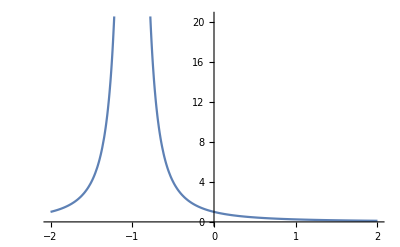

```mathematica
fn=1/(x+1)^2;
Plot[fn,{x,-2,2}]
```

```mathematica
FunctionSingularities[fn,x]
```

x==-1

```mathematica
FunctionMonotonicity[{fn,x>0},x]
```

-1

```mathematica
FunctionMonotonicity[{fn,x<-1.2},x]
```

1

### Significantly Improved Calculus

```mathematica
DSolveValue[y''[x]+(a x^4+b x^3+c x^2+d x+e)/x^4 y[x]==0,y[x],x]
```

ⅇ^(-(ⅈ √e)/x+ⅈ √a x) x^(1+(ⅈ d)/(2 √e)) C[2] HeunD[(d^2-2 ⅈ d √e-4 c e+8 √a e^(3/2))/(4 e),b+√a (2 ⅈ-d/(√e)),2 ⅈ √e,2+(ⅈ d)/(√e),2 ⅈ √a,x]+ⅇ^((ⅈ √e)/x-ⅈ √a x) x^(1-(ⅈ d)/(2 √e)) C[1] HeunD[(d^2+2 ⅈ d √e-4 c e+8 √a e^(3/2))/(4 e),b+√a (-2 ⅈ-d/(√e)),-2 ⅈ √e,2-(ⅈ d)/(√e),-2 ⅈ √a,x]

```mathematica
InverseLaplaceTransform[(-1+ⅇ^s-s)/((-1+ⅇ^s) s^2),s,t]
```

1/2-t-1/2 (-1+t) t+1/2 t (1+t)-(Piecewise[{{-(ⅈ ⅇ^(2 ⅈ n π t))/(2 n π), n≠0}, {0, True}}])n-∞∞

#### New functions: Lame functions, JacobiEpsilon, JacobiZN

### More Asymptotics

AsymptoticProbability, AsymptoticExpectation

### More Optimization

ParametricConvexOptimization, RobustConvexOptimization, (general) ConvexOptimization

## PDE Modeling Language

Building blocks for modeling sound, heat, diffusion and convection

Applications in engineering, physics, chemistry, …

#### Basic building blocks

Partial differential equations of the form ∇·(-c ∇u-α u+γ)+β·∇u+a u=f

DiffusionPDETerm—model diffusion with ∇·(-c∇u)

ConvectionPDETerm—model convection with β·∇u

ReactionPDETerm—model reaction with a u

SourcePDETerm—model a source with f

ConservativeConvectionPDETerm—model conservative convection with ∇·(-α u)

DerivativePDETerm—model a derivative of a term with ∇·(γ)

#### Named partial differential equation terms

LaplacianPDETerm—model with ∇^2 u

PoissonPDEComponent—model with ∇^2 u-f

HelmholtzPDEComponent—model with ∇^2 u+k^2 u

WavePDEComponent—model with ∂u^2/∂t^2-c^2∇^2 u

#### Acoustic PDE components

Acoustic PDE Models guide page

AcousticPDEComponent—model acoustics in the time or frequency domain

AcousticAbsorbingValue, AcousticImpedanceValue, AcousticNormalVelocityValue

AcousticPressureCondition, AcousticRadiationValue, AcousticSoundHardValue, AcousticSoundSoftCondition

Acoustics in the Time Domain—monograph about modeling acoustics in the time domain

Acoustics in the Frequency Domain—monograph about modeling acoustics in the frequency domain

#### Heat transfer PDE components

Heat Transfer PDE Models guide page

HeatTransferPDEComponent—model heat transfer

HeatFluxValue, HeatInsulationValue, HeatOutflowValue, HeatRadiationValue

HeatSymmetryValue, HeatTemperatureCondition, HeatTransferValue

Heat Transfer—monograph about modeling heat transfer

Heat Transfer Model Verification—test suite with heat transfer model verification

#### Mass transport PDE components

Mass Transport PDE Models guide page

MassTransportPDEComponent—model mass transport

MassConcentrationCondition, MassFluxValue, MassImpermeableBoundaryValue

MassOutflowValue, MassSymmetryValue, MassTransferValue

Mass Transport—monograph about modeling mass transport

```mathematica
NotebookPut[NotebookGet[]/.{"GuideFunctionsSubsection"->"Subsubsection",("GuideText"|"InlineGuideFunctionListing")->"Text"}]
```

z53ij_shm360FrontEndObject[LinkObject["z53ij_shm", 3, 1]]360Untitled-9

#### Example: Acoustics

Describe a sound wave hitting a hard boundary:

```mathematica
vars={p[t,x],t,{x}};
pars=<|"SoundSpeed"->343,"MassDensity"->1.2|>;
eqn=AcousticPDEComponent[vars,pars]==AcousticSoundHardValue[x==1,vars,pars]
```

```mathematica
p0=D[0.125 Erf[(x-0.5)/0.15],x];
ics={p[0,x]==p0,Derivative[1,0][p][0,x]==-343*D[p0,x]};
pfun=NDSolveValue[{eqn,ics},p,{t,0,0.003},x∈Line[{{0},{1}}]];
Manipulate[Plot[pfun[t,x],{x,0,1},],{{t,0},0,0.003,10^-4},]
```

## Language

### Error-Handling Tools

```mathematica
f[x_]:=If[x<0,$Failed,1/x]
```

```mathematica
g[x_]:=Enclose[1+Confirm[f[x]]]
```

```mathematica
g[-3]
```

```mathematica
g[x_]:=Enclose[1+ConfirmQuiet[f[x]]]
```

```mathematica
g[0]
```

```mathematica
g[x_]:=Enclose[1+ConfirmMatch[f[x],_Real]]
```

```mathematica
g[a]
```

### Robustness Tools

```mathematica
x=0;Pause[5];Clear[x]
```

```mathematica
WithCleanup[x=0, Pause[5],Clear[x]]
```

## Remote Batch Processes

AWS and CharityEngine support for batch evaluation

Transferable Wolfram Engine™ activation

#### Examples

```mathematica
env=RemoteBatchSubmissionEnvironment["AWSBatch",<|
"JobQueue"->"arn:aws:batch:us-east-1:123456789012:job-queue/MyQueue",
"JobDefinition"->"arn:aws:batch:us-east-1:123456789012:job-definition/MyDefinition:1",
"IOBucket"->"my-job-bucket"
|>]
```

RemoteBatchSubmissionEnvironment[…]

```mathematica
job=RemoteBatchSubmit[
env,
2+2
]
```

```mathematica
job["EvaluationResult"]
```

4

```mathematica
CreateLicenseEntitlement[]
```

LicenseEntitlementObject[…]

## I/O

Significant update of PDF import

Archive formats: 7z, ISO, RAR, ZSTD, TAR

Security certificates: PEM

MicrocontrollerEmbedCode: 36 new hardware targets

 "ArduinoZero"  ▪  "ArduinoMKRZero"  ▪  "ArduinoNano33IoT"  ▪  "ArduinoMKRWiFi1000"  ▪  "ArduinoMKRWiFi1010"  ▪  "ArduinoMKRWAN1300"  ▪  "ArduinoMKRWAN1310"  ▪  "ArduinoMKRNB1500"  ▪  "ArduinoMKRGSM1400"  ▪  "ArduinoMKRFOX1200"  ▪  "ArduinoMKRVidor4000"  ▪  "AdafruitFeatherM0BasicProto"  ▪  "AdafruitFeatherM0Express"  ▪  "AdafruitMetroM0Express"  ▪  "AdafruitCircuitPlaygroundExpress"  ▪  "AdafruitGemmaM0"  ▪  "AdafruitTrinketM0"  ▪  "AdafruitItsyBitsyM0"  ▪  "AdafruitHallowingM0"  ▪  "AdafruitMetroM4"  ▪  "AdafruitGrandCentralM4"  ▪  "AdafruitItsyBitsyM4"  ▪  "AdafruitFeatherM4Express"  ▪  "AdafruitMetroM4AirLift"  ▪  "AdafruitHallowingM4"  ▪  "AdafruitMonsterM4SK"  ▪  "SparkFunSAMD21DevBreakout"  ▪  "SparkFunSAMD21MiniBreakout"  ▪  "SparkFunLilyPadLilyMini"  ▪  "SparkFun9DoFRazorIMUM0"  ▪  "SparkFunProRF"  ▪  "SparkFunRedBoardTurbo"  ▪  "SparkFunQwiicMicro"  ▪  "MSP432P401RLaunchPad"  ▪  "ArduinoMega2560"  ▪  "ArduinoDue"

ExternalEvaluate supports SQL

```mathematica
ExternalEvaluate["SQL","select * from offices"]
```

## New in the Wolfram Language 12.2

228 new functions

Two new computational domains

Many enhancements to existing functionality

Some UI improvements